# Quantum Oracle: Definition

This  is  a demonstration material accompanying the corresponding YouTube video.

Episode 26. Classical Oracle

Episode 27. Quantum Oracle: Definition

Episode 28. Quantum Oracle: Properties

## Classical Oracle: Review

-Graphics-

Figure 1. (Left) A circuit diagram of classical oracle f:{0,1}^m→{0,1}^n. x is an m-bit string, x∈{0,1}^m, and z denotes the image of f at x, z=f(x)∈{0,1}^n. (Right) A reversible version of classical oracle f:{0,1}^m→{0,1}^n.  x∈{0,1}^m and y∈{0,1}^n are m-bit and n-bit strings, respectively, and z=f(x)∈{0,1}^n denotes the image of f at x.

### Example

```mathematica
$m=3;
$n=2;
```

```mathematica
f[1]=f[2]=3;
f[7]=2;
f[_Integer]=0;
```

```mathematica
orc=Oracle[f,$m,$n]
```

```mathematica
xx=Tuples[{0,1},$m]
```

```mathematica
zz=orc/@xx
```

```mathematica
Thread[xx->zz]//TableForm
```

## Quantum Oracle

### Definition

The quantum oracle corresponding to the classical oracle f is simply an implementation of the above extended mapping for reversible computation on quantum registers. It is a quantum gate operation defined by the association

U_f:x⊗y↦x⊗f(x)⊕y ,

where x and y are the computational basis states belonging to the native and auxiliary register of m and n qubits, respectively.

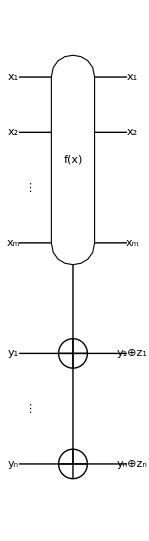

Figure 3. A quantum circuit for the quantum oracle corresponding to classical oracle f:{0,1}^m→{0,1}^n., which is a direct analogue of the classical reversible oracle in Figure 2.  x∈{0,1}^m and y∈{0,1}^n is m-bit and n-bit strings, respectively, and z=f(x)∈{0,1}^n denotes the image of f at x.

Since the extended mapping is one-to-one and the computational basis states are orthonormal, the operator U_f is unitary.

Recall that U_f is a linear operator and can act on any arbitrary superposition states.

### Example

```mathematica
Let[Qubit,S,T]
```

```mathematica
SS=S[Range[$m],$]
TT=T[Range[$n],$]
```

```mathematica
op=Oracle[f,SS,TT]
```

Note:  Oracle[f,{c_1,c_2,…},{t_1,t_2,…}] represents quantum oracle while  Oracle[f,m,n] refers to the  classical oracle.

```mathematica
qc=QuantumCircuit[op]
```

```mathematica
in=Basis[SS,TT];
ProductForm[in,{SS,TT}]
```

```mathematica
out=op**in;
ProductForm[out,{SS,TT}]
```

```mathematica
ProductForm[Thread[in->out],{SS,TT}]//TableForm
```

Compare the above result with the result from the classical oracle.

```mathematica
Thread[xx->zz]//TableForm
```

## Summary

### Keywords

Oracle

Quantum oracle

Quantum decision making

### Functions

Oracle

ControlledExp

### Related Links

Section 4.2 of the Quantum Workbook (2022, 2023).

Tutorial: Quantum Oracle

Tutorial: Quantum Decision Algorithms

Full List of Demonstrations in YouTube Videos